```mathematica
Quit[];
```

```mathematica
Needs["NDSolve`FEM`"]
toMesh[Nr_,Nz_]:=Module[{tlist={}},Do[Do[AppendTo[tlist,{ir * Nz+iz,(ir +1)* Nz+iz+1,(ir +1)* Nz+iz}+1];
AppendTo[tlist,{ir * Nz+iz,ir * Nz+iz+1,(ir +1)* Nz+iz+1}+1];,{iz,0,Nz - 1-1}],{ir,0,Nr-1-1}];
tlist]
SetDirectory[NotebookDirectory[]];
```

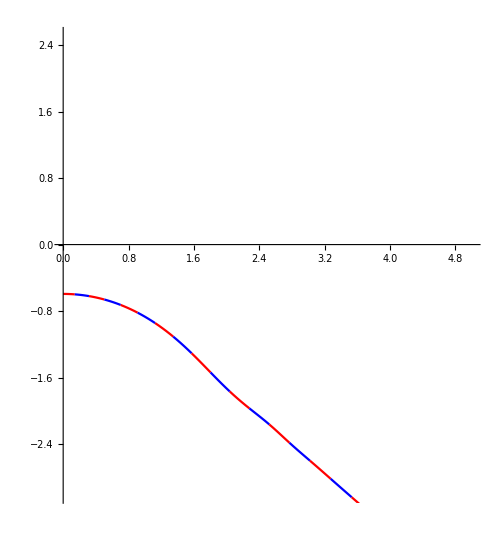

```mathematica
sp0=Import["sp0.txt","Table"];
sp1=Import["sp1.txt","Table"];
n0 = (Length@sp0+1)/3;
n1 = (Length@sp1+1)/3;
cx=Join[sp0⟦1;;n0⟧,sp1⟦1;;n1⟧];
cy=Join[sp0⟦n0+1;;n0*2⟧,sp1⟦n1+1;;n1*2⟧];
h=Join[sp0⟦2 n0+1;;-1⟧,sp1⟦2n1+1;;-1⟧];
dKv=0.0005;
Subscript[sx, i_][t_?NumberQ]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_?NumberQ]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
(*Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,40,1}];*)
Table[{Subscript[sx, i][#],Subscript[sy, i][#]}&/@Range[0,1,0.2],{i,1,30}];
tt=ListPlot[%,AspectRatio->Automatic,Joined->True,PlotStyle->{Red,Blue}];
Show[%,AspectRatio->Automatic,ImageSize->500,PlotRange->{{0,5},{-4,1.5}+1}]
```

```mathematica
field=Import["../Output/field.txt","Table"];Length@field
If[Length@field>0,
fieldCoord = field⟦All,{1,2}⟧;
fieldValue =field⟦All,3⟧;
fieldValueDr =field⟦All,4⟧;
fieldValueDz =field⟦All,5⟧;
fieldBoundary =Flatten[ Table[{Subscript[sx, i][#],Subscript[sy, i][#]}&/@Range[dKv,1+dKv,0.1],{i,1,50}],1];
fieldBoundaryFunction=Interpolation[fieldBoundary,InterpolationOrder->4];
mesh=ToElementMesh["Coordinates"->fieldCoord,"MeshElements"->{TriangleElement[toMesh[100,80]]}];
fieldFunction=ElementMeshInterpolation[{mesh},fieldValue];
fieldDrFunction=ElementMeshInterpolation[{mesh},fieldValueDr];
fieldDzFunction=ElementMeshInterpolation[{mesh},fieldValueDz];]
```

8000

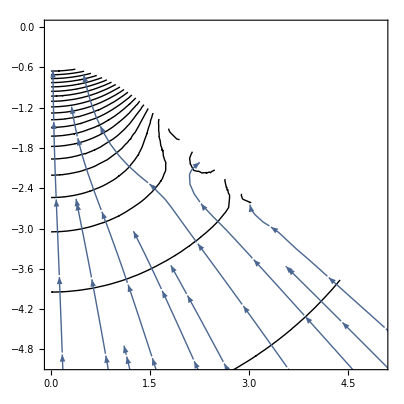

```mathematica
cPlot=ContourPlot[fieldFunction[a,b],{a,b}∈mesh,PlotRange->All,PlotPoints->50,
PerformanceGoal->"Quality",Contours->20,RegionFunction->Function[{a,b},b>-6],ContourShading->None];
sPlot=StreamPlot[{fieldDrFunction[a,b],fieldDzFunction[a,b]},{a,b}∈mesh,StreamPoints->1000,
PerformanceGoal->"Quality",RegionFunction->Function[{a,b},-6<b<fieldBoundaryFunction[a]-0.05]];
(*bPlot=Plot[Evaluate@fieldBoundaryFunction[t],{t,0,xMax},PlotStyle->plotStyle];*)
Show[cPlot,sPlot,AspectRatio->Automatic,PlotRange->{{0,5},{-4,1}-1}]
```

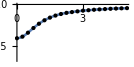
```mathematica
Clear[i,kv,kvt];dKv=0.00005;
last=-Graphics-;
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];//Quiet;
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5+Subscript[sy, i]'[t]/Subscript[sx, i][t]/√((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)
Flatten[Table[{Subscript[sx, i][#],Subscript[kv, i][#]}&/@Range[dKv,1+dKv,0.1],{i,1,40}],1];
Show[last,ListPlot[%,Joined->True,PlotRange->All],Graphics[{Red,Point@%⟦1;;-1;;10+1⟧}],AspectRatio->0.5,PlotRange->{{0,5},{-1.5,0.1}}]
```

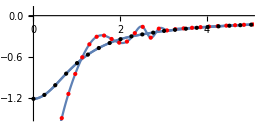

```mathematica
c0=-0.86043668612567826958329232241006895090205537938856512312860301418123537837128`49.759363080297355;
c1 = -0.875880000000000;
b0=+1.759300000000000;
c3=-0.282848756957467;
nrz = Normalize@Grad[(z-cc0 r),{r,z}];
b0 (r^2+z^2)^(1/4)LegendreP[1/2,z/(r r + z z)^(1/2)]+b1/√(r^2+z^2);
Grad[%,{r,z}].nrz;
%/.{cc0->c0};
Series[%/.z->c0 r,{r,∞,2}]
b1r = CoefficientList[%,r^(-1/2)]⟦2⟧
```

1.49291 √(1/r)+O[1/r]^(5/2)

1.49291

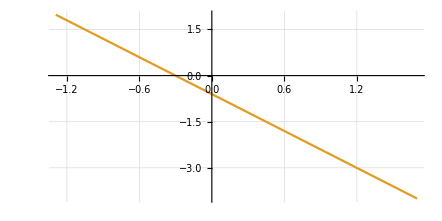

```mathematica
res=Import["res.txt","Table"];
Clear[xc,psin]
xc = res⟦2;;-1,1⟧;
psin = res⟦2;;-1,2⟧;
ListPlot[Log10@Abs@{Transpose[{xc,psin+b1r/√xc }],
Transpose[{xc,0.25 xc^-2}]}
,PlotRange->All,Joined->True,AspectRatio->0.5,GridLines->Automatic]
(*LinearModelFit[Log10@Abs[Transpose[{xc,psin +1.4929102712340343/√xc}]⟦2;;5⟧],t,{t}]*)
(*Subscript[kv, 1][10^-5.]/2
res⟦1,2⟧/2*)
```

```mathematica
+1.760000000000000
```

FittedModel[0.140875-0.47498 t]

-0.604992

-0.91957

FittedModel[-0.0575583-0.499998 t]

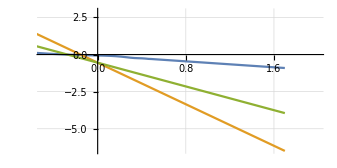

```mathematica
xx=cx⟦2;;n0,1⟧;
yy=cy⟦2;;n0,1⟧;
Log10@Abs@Transpose[{xx,yy-c0 xx-c1/√xx}];
LinearModelFit[%⟦n0-150;;n0-50⟧,t,{t}]
ListPlot[Log10@Abs@{Transpose[{xx,yy-c0 xx-c1/√xx}],
Transpose[{xx,c3 /xx^3.5}],Transpose[{xx,c3 /xx^2}]
},Joined->{True,True},GridLines->Automatic,AspectRatio->0.5,PlotRange->{{-0.5,2},Automatic}]
```

```mathematica
"
```

```mathematica
Log10@1.6
```

0.20412

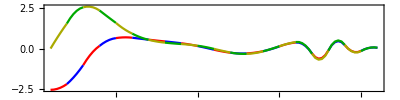

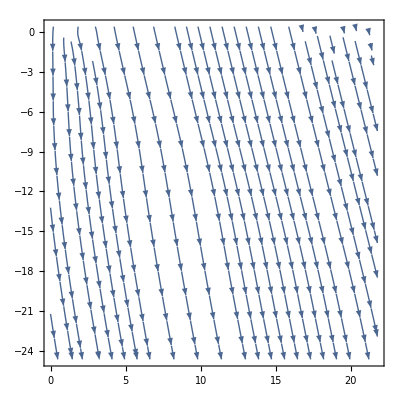

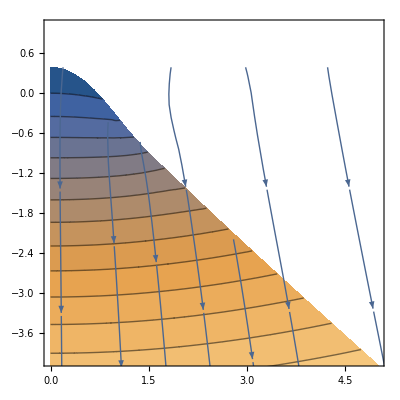

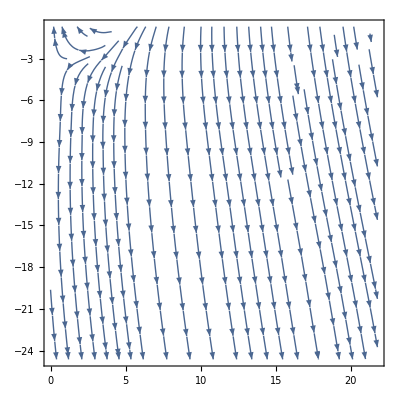

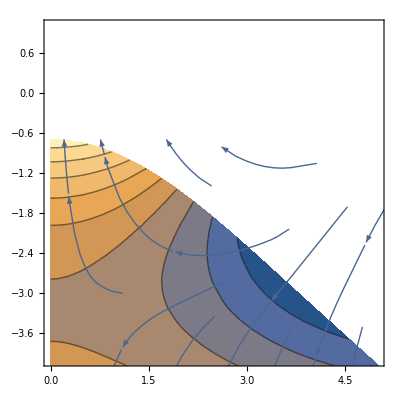

```mathematica
dv=3;
trange = Join[Range[1,n0-1],Range[n0+1,n0+n1 -2]];
trange =Range[1,20];
tx = Table[Flatten@{(#+i),Derivative[dv][Subscript[sx, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.2],{i,trange}];
ty = Table[Flatten@{#+i,Derivative[dv][Subscript[sy, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.2],{i,trange}];
(*ty = Table[{t+i,Derivative[dv][Subscript[sy, i]][t]/h⟦i⟧^dv},{i,1,Length@cx-1}];*)
Show[
ListPlot[tx,PlotStyle->{Red,Blue},Joined->True,PlotRange->All],
ListPlot[ty,PlotStyle->Darker@{Yellow,Green},Joined->True,PlotRange->All]
,PlotRange->All,(*ParametricPlot[{ty⟦1⟧,ty⟦2⟧},{t,0,1}],*)
AspectRatio->0.25,Frame->True]
```

{496.627,496.629,496.627,496.627,496.627,496.625,496.632,496.616,496.612,496.625,496.625,496.625,496.633,496.627,496.625,496.627,496.625}

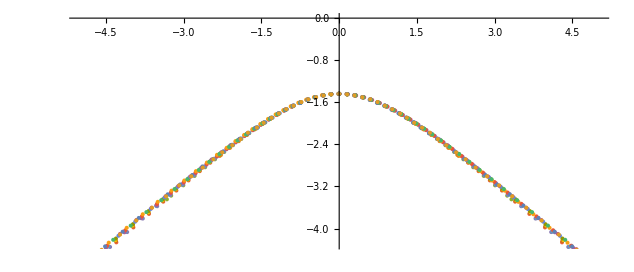

```mathematica
SetDirectory[NotebookDirectory[]];
bt=Import["C:\\Users\\czhou\\Documents\\LIS2T\\Preprint\\TaylorCone\\Resources\\DataFromBurtonPaper\\*.txt","Table","FieldSeparators"->","]⟦1;;-3⟧;
bt = DeleteDuplicatesBy[#,First]&/@bt;
origin=531.59;
ListPlot@bt;
shiftx = Interpolation[DeleteDuplicatesBy[#,First],InterpolationOrder->4]&/@bt;
findx=(t/.FindRoot[#'[t]==0,{t,497},WorkingPrecision->MachinePrecision])&/@shiftx
Do[bt⟦i,All,1⟧=bt⟦i,All,1⟧ - findx⟦i⟧ ;
bt⟦i,All,2⟧=bt⟦i,All,2⟧ - origin;,{i,1,Length@bt}]
intbt=Interpolation[DeleteDuplicatesBy[#,First],InterpolationOrder->3][0]&/@bt;
Do[bt⟦i,All,1⟧=bt⟦i,All,1⟧ /Abs@intbt⟦i⟧;bt⟦i,All,2⟧=bt⟦i,All,2⟧ /Abs@intbt⟦i⟧;,{i,1,Length@bt}];
ListPlot[bt,AspectRatio->Automatic,Joined->True,PlotRange->{8{-1,1},8*0.86{-1,0}}];
scale= Abs@Subscript[sy, 1][0];btScale = bt;
Do[btScale⟦i,All,1⟧=bt⟦i,All,1⟧ *scale;btScale⟦i,All,2⟧=bt⟦i,All,2⟧ *scale;,{i,1,Length@bt}]
Show[ListPlot[btScale,AspectRatio->Automatic,PlotRange->{5{-1,1},5*0.86{-1,0}}]]
```

```mathematica
toMesh[Nr_,Nz_]:=Module[{tlist={}},
Do[Do[AppendTo[tlist,{ir * Nz+iz,(ir +1)* Nz+iz+1,(ir +1)* Nz+iz}+1];
AppendTo[tlist,{ir * Nz+iz,ir * Nz+iz+1,(ir +1)* Nz+iz+1}+1];
,{iz,0,Nz - 1-1}]
,{ir,0,Nr-1-1}];
tlist]
```